### Problem 1

```mathematica
D[V[t,S],t]+1/2 S^2 σ^2 D[V[t,S],{S,2}]+S (r-𝔻)D[V[t,S],S]-r V[t,S]==0
```

```mathematica
Subscript[Vcall, k_,T_,σ_,r_,𝔻_][t_,S_]:=
1/2 ⅇ^(r(t-T))(ⅇ^((-t+T)(r-𝔻))S (1+Erf[(-(t-T)(2(r-𝔻)+σ^2)+2Log[S/k])/(2 √2 √((-t+T)σ^2))])+k(-2+Erfc[(-(t-T)(2(r-𝔻)-σ^2)+2Log[S/k])/(2 √2 √((-t+T)σ^2))]))
```

```mathematica
Subscript[Vput, k_,T_,σ_,r_,𝔻_][t_,S_]:=
1/2 ⅇ^(r(t-T))(k Erfc[(-(t-T)(2(r-𝔻)-σ^2)+2Log[S/k])/(2 √2 √((-t+T)σ^2))]-ⅇ^((-t+T)(r-𝔻))S Erfc[(-(t-T)(2(r-𝔻)+σ^2)+2Log[S/k])/(2 √2 √((-t+T)σ^2))])
```

```mathematica
VC[t_,S_]:=Subscript[Vcall, k,T,σ,r,𝔻][t,S]
```

```mathematica
VP[t_,S_]:=Subscript[Vput, k,T,σ,r,𝔻][t,S]
```

```mathematica
D[VC[t,S],t]+1/2 S^2 σ^2 D[VC[t,S],{S,2}]+S (r-𝔻)D[VC[t,S],S]-r VC[t,S]==0//Simplify
```

True

```mathematica
D[VP[t,S],t]+1/2 S^2 σ^2 D[VP[t,S],{S,2}]+S (r-𝔻)D[VP[t,S],S]-r VP[t,S]==0//Simplify
```

True

### Problem 2

```mathematica
Subscript[Vcall, 75,25/365,.3,.03,.02][0,75]
```

2.37029

```mathematica
Subscript[Vput, 75,25/365,.3,.03,.02][0,75]
```

2.31901

### Problem 3

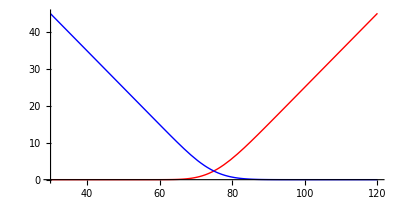

```mathematica
Plot[{Subscript[Vcall, 75,25/365,.3,.03,.02][0,S],Subscript[Vput, 75,25/365,.3,.03,.02][0,S]},{S,30,120},AspectRatio-> Automatic,PlotStyle-> {Red,Blue}]
```

### Problem 4

```mathematica
-150Derivative[0,1][Subscript[Vcall, 75,25/365,.3,.03,.02]][0,75]
```

-77.7635

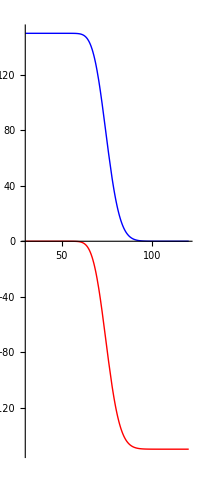

```mathematica
Plot[{-150Derivative[0,1][Subscript[Vcall, 75,25/365,.3,.03,.02]][0,S],-150Derivative[0,1][Subscript[Vput, 75,25/365,.3,.03,.02]][0,S]},{S,30,120},AspectRatio-> Automatic,PlotStyle-> {Red,Blue}]
```

### Problem 5

```mathematica
σ[S_]:=.001 (S-70)^2+.3
```

```mathematica
BSPDE=D[V[t,S],t]+1/2 S^2 σ[S]^2 D[V[t,S],{S,2}]+S (r-𝔻)D[V[t,S],S]-r V[t,S]==0
```

-r V[t,S]+S (r-𝔻) V^(0,1)[t,S]+1/2 (0.3+0.001 (-70+S)^2)^2 S^2 V^(0,2)[t,S]+V^(1,0)[t,S]==0

### Problem 6

```mathematica
k=75;T=25/365;σ=.3;r=.03;𝔻=.02;S0=30;S1=120;
```

```mathematica
callpayoff[S_]:=Max[S-k,0]
putpayoff[S_]:=Max[k-S,0]
```

```mathematica
Off[NDSolve::mxsst]
```

```mathematica
call[t_,S_]=V[t,S]/.NDSolve[Join[{BSPDE,V[T,S]==callpayoff[S]},{V[t,S0]==callpayoff[S0],V[t,S1]==callpayoff[S1]}],V[t,S],{t,0,T},{S,S0,S1}][[1]]
```

InterpolatingFunction[{{0.,0.0684932},{30.,120.}},<>][t,S]

```mathematica
call[0,75]
```

2.61944

```mathematica
put[t_,S_]=V[t,S]/.NDSolve[Join[{BSPDE,V[T,S]==putpayoff[S]},{V[t,S0]==putpayoff[S0],V[t,S1]==putpayoff[S1]}],V[t,S],{t,0,T},{S,S0,S1}][[1]]
```

InterpolatingFunction[{{0.,0.0684932},{30.,120.}},<>][t,S]

```mathematica
put[0,75]
```

2.56816

### Problem 7

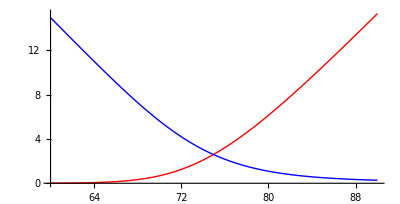

```mathematica
Plot[{call[0,S],put[0,S]},{S,60,90},AspectRatio-> Automatic,PlotStyle-> {Red,Blue}]
```

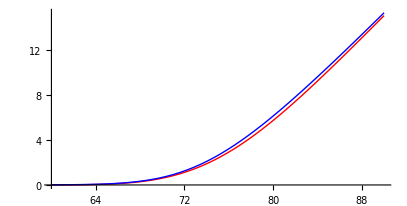

```mathematica
Plot[{Subscript[Vcall, 75,25/365,.3,.03,.02][0,S],call[0,S]},{S,60,90},AspectRatio-> Automatic,PlotStyle-> {Red,Blue}]
```

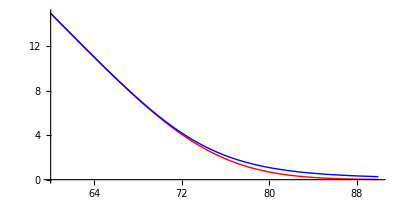

```mathematica
Plot[{Subscript[Vcall, 75,25/365,.3,.03,.02][0,S],call[0,S]},{S,60,90},AspectRatio-> Automatic,PlotStyle-> {Red,Blue}]
```

### Problem 8

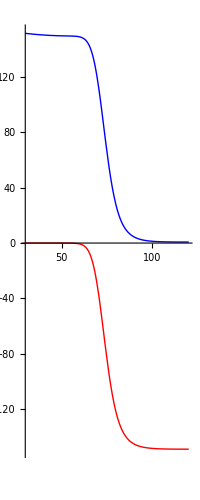

```mathematica
Plot[{-150Derivative[0,1][call][0,S],-150Derivative[0,1][put][0,S]},{S,30,120},AspectRatio-> Automatic,PlotStyle-> {Red,Blue}]
```

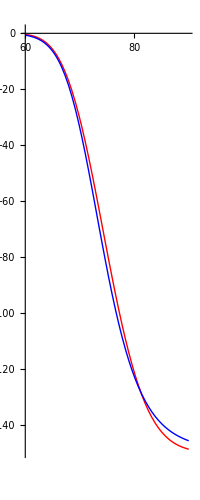

```mathematica
Plot[{-150Derivative[0,1][Subscript[Vcall, 75,25/365,.3,.03,.02]][0,S],-150Derivative[0,1][call][0,S]},{S,60,90},AspectRatio-> Automatic,PlotStyle-> {Red,Blue}]
```

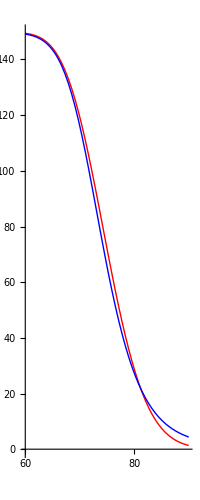

```mathematica
Plot[{-150Derivative[0,1][Subscript[Vput, 75,25/365,.3,.03,.02]][0,S],-150Derivative[0,1][put][0,S]},{S,60,90},AspectRatio-> Automatic,PlotStyle-> {Red,Blue}]
```